```mathematica
SetDirectory[NotebookDirectory[]];
ClearAll["Global`*"]
```

```mathematica
trueDist = NormalDistribution[5,2];
felpd1[aDist_,aDist1_]:=Expectation[N@Log[PDF[aDist,x]],x\[Distributed]aDist1]
aList=ParallelTable[{μ,felpd1[NormalDistribution[μ,2],trueDist]},{μ,1,9,2}];
cList=Table[PDF[NormalDistribution[μ,2],x],{μ,1,9,2}];
```

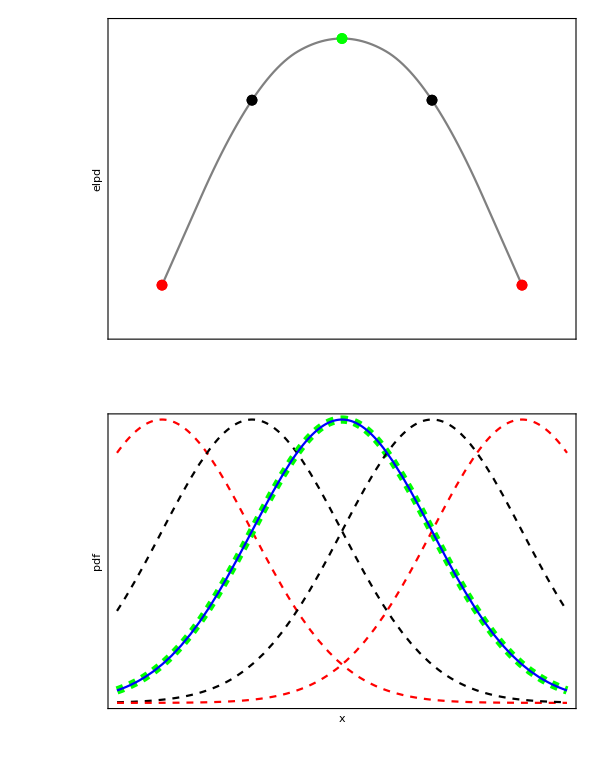

```mathematica
{yMin,yMax}  = {-4.5,-2};
g1=Show[ListLinePlot[aList,PlotRange->{{0,10},{yMin,yMax}},InterpolationOrder->2,PlotStyle->Gray,Frame->{True,True,False,False},FrameTicks->{None,None},FrameLabel->{"","elpd"},BaseStyle->{FontSize->16}],ListPlot[{aList[[1]]},PlotRange->{{0,10},{yMin,yMax}},PlotStyle->Red,Frame->{True,True,False,False},FrameTicks->{None,None},FrameLabel->{"","elpd"},BaseStyle->{FontSize->16}],ListPlot[{aList[[2]]},PlotRange->{{0,10},Full},PlotStyle->Black],ListPlot[{aList[[3]]},PlotRange->{{0,10},Full},PlotStyle->Green],ListPlot[{aList[[4]]},PlotRange->{{0,10},Full},PlotStyle->Black],ListPlot[{aList[[5]]},PlotRange->{{0,10},Full},PlotStyle->Red]];
g2=Show[Plot[cList,{x,0,10},PlotStyle->{{Dashed,Red},{Dashed,Black},{Dashed,Green,Thickness[0.015]},{Dashed,Black},{Dashed,Red}},Frame->{True,True,False,False},FrameTicks->{None,None},FrameLabel->{"x","pdf"},BaseStyle->{FontSize->16}],Plot[PDF[trueDist,x],{x,0,10},PlotStyle->Blue]];
gFinal=Show[GraphicsColumn[{g1,g2}],ImageSize->600]
```

```mathematica
Export["Evaluation_elpd.pdf",gFinal]
```

Evaluation_elpd.pdf